```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*tab=Import["testdata_mat.txt","Table"];*)
tab=Import["K_Xe_v_6_hp_orth_mat.txt","Table"];
Evalues = tab[[7]];
qvalues = tab[[10]];
Kvalues=tab[[13;;]];
EMIN=Min[Evalues];
EMAX=Max[Evalues];
QMIN=Min[qvalues];
QMAX=Max[qvalues];
KEvalues[NE_]:=Transpose[{qvalues,Kvalues[[NE]]}]
```

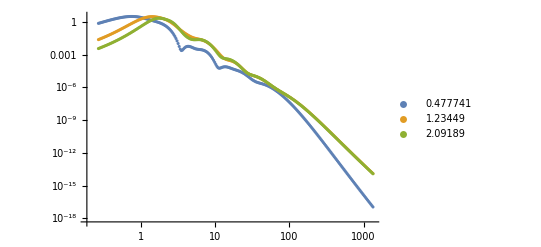

```mathematica
ListLogLogPlot[{KEvalues[1],KEvalues[10],KEvalues[15]},PlotLegends->{Evalues[[1]],Evalues[[10]],Evalues[[15]]}]
```

### Interpolate (in log-log space)

```mathematica
loglogdata=Flatten[Table[{{Log[Evalues[[i]]],Log[qvalues[[j]]]},Log[Kvalues[[i,j]]]},{i,1,Length[Evalues]},{j,1,Length[qvalues]}],1];
loglogKion = Interpolation[loglogdata];
Kion[dE_,q_]:=If[EMAX>dE>EMIN &&QMAX>q>QMIN , Exp[loglogKion[Log[dE],Log[q]]],0.0]
```

#### Test interpolated function:

5.70665

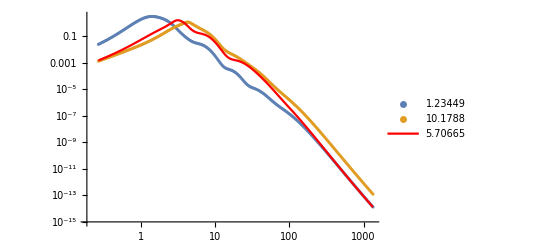

```mathematica
Eindex=10;
Emid=(0.5Evalues[[Eindex]]+0.5Evalues[[Eindex+20]])
Show[ListLogLogPlot[{KEvalues[Eindex],KEvalues[Eindex+20]},PlotLegends->{Evalues[[Eindex]],Evalues[[Eindex+20]]}],LogLogPlot[Kion[Emid,q],{q,QMIN,QMAX},PlotStyle->Red,PlotLegends->{Emid}]]
```

```mathematica
qminus[e_,de_]:=√(2.0 e)-√(2.0(e-de))
qplus[e_,de_]:=√(2.0 e)+√(2.0(e-de))
a02=0.0279841;
σ[Ei_]:=(4π)/Ei a02 NIntegrate[Kion[Ei,q]/q^3,{dE,0,Ei},{q,qminus[Ei,dE],qplus[Ei,dE]}]
```

```mathematica
σiontab=Table[{27.277*10^le,σ[10^le]},{le,Log10[10.0/27.211],Log10[1000.0/27.211],0.05}];//Quiet
```

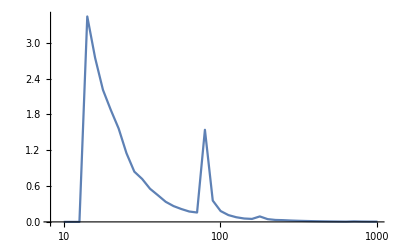

```mathematica
ListLogLinearPlot[σiontab,PlotRange->All,Joined->True]
```

```mathematica
Length[σiontab]
```

41

```mathematica
299792458/1000.0
```

299792.